## Первое приближение

```mathematica
ν0 = (3. 10^8)/(670 10^-9)/10^6; (* МГц *)
c = 3 10^8; (* м/c *)
Γ = 6 10^6 /10^6(* МГц *);
vQ = 1200; (* м/c *)
```

```mathematica
ClearAll[f1];
f1[s_, ν_] := f1[s, ν] = NIntegrate[
(1-s/(1 +s+ 4 (ν - ν0(1+ v/c))^2/Γ^2))
1/(1  + 4 (ν - ν0(1- v/c))^2/Γ^2)Exp[- v^2/vQ^2], {v, -2 vQ, + 2 vQ}, MaxRecursion->12];
```

```mathematica
ϵ =4 10^-8;
image1 = Show[{
DiscretePlot[
{-f1[100, ν0+ν], -f1[10, ν0+ν], -f1[1, ν0+ν], -f1[1/2, ν0+ν], -f1[0, ν0+ν]}, {ν,- ϵ ν0, 0, ϵ ν0 / 100}, 
PlotStyle->{, ,,,{Black, Dashed}}, PlotRange->{{-10, 5}, {-7, 0}}, Filling->None, 
PlotLabels->{"s=100", "s=10", "s=1", "s=1/2"}, Joined->True, AxesLabel->{"ν, МГц", "~ Log[I_out/I_in]"}, AspectRatio->3/2]
, DiscretePlot[
{-f1[100, ν0+ν], -f1[10, ν0+ν], -f1[1, ν0+ν], -f1[1/2, ν0+ν], -f1[0, ν0+ν]}, {ν,- ϵ ν0, + ϵ ν0, ϵ ν0 / 100}, 
Filling->None, Joined->True, PlotStyle->{, ,,,{Black, Dashed}}]
}]
```

-Graphics-

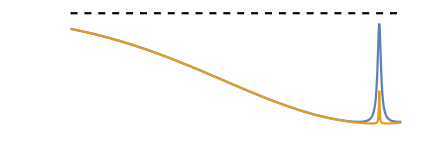

```mathematica
ϵ =8 10^-6;
image2 = DiscretePlot[
{-f1[100, ν0+ν], -f1[1, ν0+ν],0}, {ν,- 0.7ϵ ν0, +ϵ ν0/20, ϵ ν0 / 1000}, PlotRange->Full,Filling->None, Joined->True, PlotStyle->{,,{Dashed, Black}},AxesLabel->{"ν, МГц", "~ Log[I_out/I_in]"}, Axes->False, AspectRatio->1/3]
```

```mathematica
(*Export[NotebookDirectory[]<>"v2.png", image2]*)
```

## Оценка κ

```mathematica
kB= 1.38 10^-23;
ℏ = 1 10^-34;
Na = 6.02 10^23;
R = Na kB;
m = 0.007 / Na;
M = 0.007;
T = 300 + 273;
vQ = √((2 kB T)/m);
Print["<v> = ", ScientificForm[vQ, 2], " м/c"]
```

<v> = 1.2×10^3 м/c

```mathematica
ClearAll[GetP];
GetP[T_] := 133.32 10^(10.3454 -8345.57/T-8.84 10^-5 T - 0.68106 Log10[T]);
n = GetP[T]/(kB T);
Print["концентрация n = ", ScientificForm[n, 2], " (:043c)^-3"]
```

концентрация n = 1.2×10^16 м^-3

```mathematica
l = 0.1; (* м, -- область пересечения лучей *)
σ0 = 4 π(10^-10)^2;
κ = σ0 n l √(m/(2 π kB T));
Print["κ = ", ScientificForm[κ, 2], " (м/c)^-1"]
```

κ = 7.3×10^-8 (м/c)^-1

## Оценка контрастности